```mathematica
energy={1.3373202085701266,0.18643393369537004,0.07105746158595466,0.037407167983470095,0.023050971424107496,0.015618389794715332,0.005359292748188737,0.001293695341342178};
ϵ={0.8495627307374232,0.1686953413421779,0.0685023233606453,0.03671191766777224,0.022796501845899386,0.015507234864525106,0.005349562730737423,0.001293695341342178};(*the energy of perturbation*)
Ε=Join[Table[N[0.5 i^-2],{i,6}],{0.5 10^-2,0.5 20^-2}]
Lepageenergy={1.28711542,0.183325753,0.0703755485,0.0371495726,0.0229268241,0.0155492598,0.00534541931,0.0012920501};
(*Lepage's original data*)
Lepageϵ={0.8364007999999992,0.1670500999999999,0.0680148444444444,0.036506262499999984,0.022691206399999993,0.015446299999999994,0.005336400799999999,0.0012920501};
(*Lepage's first order perturbation*)
δLepage=Join[Table[Abs[(1/(2 i^2)-Lepageenergy[[i]])/Lepageenergy[[i]]],{i,6}],{Abs[(1/(2 10^2)-Lepageenergy[[7]])/Lepageenergy[[7]]]},{Abs[(1/(2 20^2)-Lepageenergy[[8]])/Lepageenergy[[8]]]}];
(*Lepage's Coulomb energy relative error*)
LδLepage=Join[Partition[(*N[1/(2#^2)]&/@{1,2,3,4,5,6,10,20}*)Lepageenergy,1],Partition[δLepage,1],2]
(*Lepage's Coulomb energy relative error and Lepageenergy cordinate*)
δLepageϵ =Table[Abs[(Lepageϵ[[i]]-Lepageenergy[[i]])/Lepageenergy[[i]]],{i,8}];
(*Lepage's first order perturbation energy relative error*)
LδLepageϵ={Lepageenergy[[#]],δLepageϵ[[#]]}&/@{1,2,3,4,5,6,7,8}
(*Lepage's first order perturbation energy relative error and Lepageenergy cordinate*)
```

{0.5,0.125,0.0555556,0.03125,0.02,0.0138889,0.005,0.00125}

{{1.28712,0.611534},{0.183326,0.318154},{0.0703755,0.210584},{0.0371496,0.158806},{0.0229268,0.127659},{0.0155493,0.106781},{0.00534542,0.0646197},{0.00129205,0.0325453}}

{{1.28712,0.350174},{0.183326,0.08878},{0.0703755,0.0335444},{0.0371496,0.0173168},{0.0229268,0.0102769},{0.0155493,0.00662152},{0.00534542,0.00168715},{0.00129205,0.}}

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]
Vs2[r_]=- α/r Erf[r/(√2 a)]+c2 a^2 δa[r]+d1 a^4 Laplacian[δa[r],{r,θ,ϕ},"Spherical"]
```

(c1 ⅇ^(-r^2/2))/(2 √2 π^(3/2))-Erf[r/(√2)]/r

(c2 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+d1 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2)))-Erf[r/(√2)]/r

```mathematica
a=1;
```

```mathematica
c2=4π*-3.18;
d1=4π*0.199;
```

```mathematica
(*Vs1's Fit for c1*)
sol1=ParametricNDSolve[{Vs1[r] f[r]-1/2 f''[r]==Lepageenergy[[8]]f[r],f[1000]==0,f'[1000]==-10^-6},f,{r,1000,10^-6},c1]
```

{f→ParametricFunction[<>]}

```mathematica
FindRoot[f[c1][0]==0/.sol1,{c1,-1}]
```

{c1→14.1515}

```mathematica
sol2a=ParametricNDSolve[{Vs2[r] f[r]-1/2 f''[r]==Lepageenergy[[7]]f[r],f[1000]==0,f'[1000]==-10^-6},f,{r,1000,10^-6},{c2,d1},MaxSteps->Infinity,WorkingPrecision->30,MaxStepFraction->10^-3,AccuracyGoal->8]
sol2b=ParametricNDSolve[{Vs2[r] f[r]-1/2 f''[r]==Lepageenergy[[8]]f[r],f[1000]==0,f'[1000]==-10^-6},f,{r,1000,10^-6},{c2,d1},MaxSteps->Infinity,WorkingPrecision->30,MaxStepFraction->10^-3,AccuracyGoal->8]
```

{f→ParametricFunction[<>]}

{f→ParametricFunction[<>]}

```mathematica
FindRoot[{f[c2,d1][10^-6]==0/.sol2a,f[c2,d1][10^-6]==0/.sol2b},{{c2,-50,-10},{d1,-20,-1}},WorkingPrecision->30,MaxIterations->100,AccuracyGoal->Infinity,PrecisionGoal->8,DampingFactor->2]
{c2/(4π),d1/(4π)}/.%
```

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

{c2→88.0131498855254671709378811507,d1→50.0235002106058689750230961966}

{7.00386393068463010672322304902,3.98074366463819571018686164014}

```mathematica
{f[c2,d1][10^-6]/.sol2a,f[c2,d1][10^-6]/.sol2b}/.%%
```

{5.5224231149425327731792967853×10^-8,0.00001306727809378034696392648214}

```mathematica
Module[{shift=10,d=2000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+(Vs2[r] /.%86)f[r]-1/2 f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift]
```

```mathematica
-3.18*4π
```

-39.9611

```mathematica
0.2*4π
```

2.51327

```mathematica
αf=2.;u0=1.*10^-8;r1=1500.;r2=u0;
```

```mathematica
sol=ParametricNDSolve[{u''[r]+(αf(e-Vs2[r])-0/r^2)u[r]==0,u[r1]==u0,u'[r1]==(*√(α(V[r1]-e)) u0*)-u0},
u,{r,r1,r2},e,Method->"Chasing",MaxSteps->Infinity,WorkingPrecision->30,MaxStepFraction->10^-3,AccuracyGoal->8]
```

{u→ParametricFunction[<>]}

```mathematica
FindRoot[u[e][r2]==0/.sol,{e,-0.00129,-0.00130},MaxIterations->10000,WorkingPrecision->30,AccuracyGoal->8]
```

{e→-0.00129203295479380250666790349671}

```mathematica
ϵ2={};
```

```mathematica
AppendTo[ϵ2,e/.%]
```

```mathematica
Lepageϵ2=-ϵ2
```

{1.49378,0.182098,0.0703401,0.0371441,0.022925,0.0155484,0.00534527,0.00129203295479380250666790349671}

```mathematica
δLepageϵ2 =Table[Abs[(Lepageϵ2[[i]]-Lepageenergy[[i]])/Lepageenergy[[i]]],{i,8}]
```

{0.160565,0.00669547,0.000503441,0.000147958,0.0000786231,0.0000547167,0.0000276332,0.0000132698}

```mathematica
LδLepageϵ2={Lepageenergy[[#]],δLepageϵ2[[#]]}&/@{1,2,3,4,5,6,7,8}
```

{{1.28712,0.160565},{0.183326,0.00669547},{0.0703755,0.000503441},{0.0371496,0.000147958},{0.0229268,0.0000786231},{0.0155493,0.0000547167},{0.00534542,0.0000276332},{0.00129205,0.0000132698}}

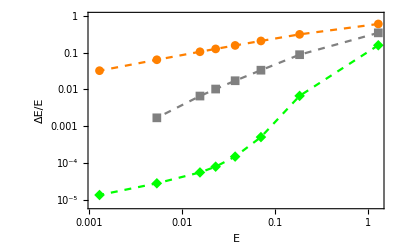

```mathematica
ListLogLogPlot[{LδLepage,LδLepageϵ,LδLepageϵ2},Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"E","ΔE/E"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},ImageSize->Full]
```